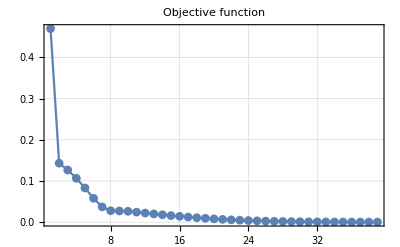

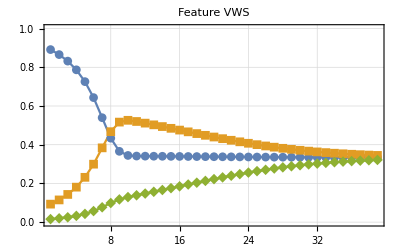

```mathematica
d=Import[NotebookDirectory[]<>"~log - vortex - fixed.txt","Table"];
ListLinePlot[d[[All,2]],PlotTheme->"Detailed",PlotLabel->"Objective function",PlotMarkers->Automatic,PlotRange->All,BaseStyle->{FontSize->14}]
ListLinePlot[Transpose@d[[All,4;;6]],PlotTheme->"Detailed",PlotLabel->"Feature VWS",PlotMarkers->Automatic,PlotRange->{All,{0,1}},BaseStyle->{FontSize->14}]
```

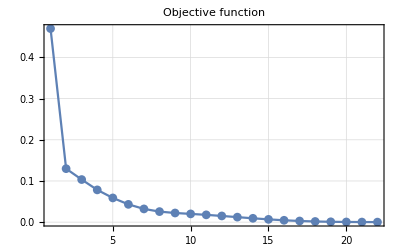

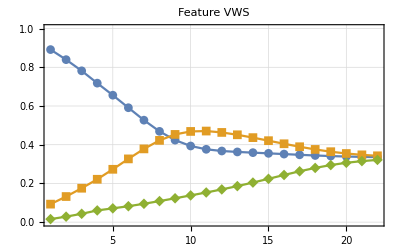

```mathematica
d=Import[NotebookDirectory[]<>"~log - vortex - linesearch.txt","Table"];
ListLinePlot[d[[All,2]],PlotTheme->"Detailed",PlotLabel->"Objective function",PlotMarkers->Automatic,PlotRange->All,BaseStyle->{FontSize->14}]
ListLinePlot[Transpose@d[[All,4;;6]],PlotTheme->"Detailed",PlotLabel->"Feature VWS",PlotMarkers->Automatic,PlotRange->{All,{0,1}},BaseStyle->{FontSize->14}]
```